## Formulae an

```mathematica
ExplainContractionCounts[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
nonEdges=0,
remainingNonEdges=0,
result},
result=Table[
If[!EdgeQ[gBis,e[[1]]<->v]&&!EdgeQ[gBis,e[[2]]<->v],
nonEdges++
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
remainingNonEdges=Length[EdgeList[comp]];
{nonEdges,remainingNonEdges}
]
```

```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3}}

```mathematica
cm=72/2.54;
```

```mathematica
Clear[MpgChain2]
```

```mathematica
SymbolToColoring[First[FindFullFormula4[Graph[plantri [[1]] ]]]]
```

{1→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],11→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],12→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],7→RGBColor[1, 1, 0],10→RGBColor[1, 1, 0],4→RGBColor[0, 1, 0],6→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0]}

```mathematica
MpgChain2[g_,glayout_:"TutteEmbedding",previous_:{}, positions_:Null,size_:{}]:=Block[{contract, result, coord, newPos=positions,newSize=size, layout, thegraph,form,graphs},
If[VertexCount[g]==2,Return[{}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
If[positions==Null,
layout = Graph[
SortGraph[g],
GraphLayout->glayout,
GraphHighlightStyle->"Thick",
ImageSize->{6 cm,6 cm}, 
VertexCoordinates->Automatic
];
newPos=First[AbsoluteOptions[layout, VertexCoordinates]][[2]];
newSize=First[AbsoluteOptions[layout, ImageSize]][[2]];
];
coord=newPos;(*Table[newPos[[k]],{k,VertexList[g]}];*)
form=FindFullFormula4[g];
If[form≠{},form=SymbolToColoring[First[form]]];
thegraph=Graph[
Range[Length[newPos]],
EdgeList[g],
GraphHighlightStyle->"Thick",
VertexLabels->Map[If[MemberQ[previous,#],#->ToString[previous],#->#]&,VertexList[g]],
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,10],
ImageSize->newSize, 
AspectRatio->1,
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->form, 
VertexSize->Map[#->If[MemberQ[previous,#],Larger[Large],Large]&,VertexList[g]],
VertexCoordinates->coord
];
result=Prepend[MpgChain2[contract,glayout,{e[[1]],e[[2]]}, newPos,newSize],{Labeled[
thegraph,{Column[ExplainContractionCounts[g,e]],Style[ChromaticPolynomial[g,4]/24,Green ],Grid[Transpose[Map[{#,VertexDegree[g,#]}&,Sort[VertexList[g]]]],Frame->All]}],
graphs=Table[
With[{sub=NeighborhoodGraph[ thegraph,v]},
Graph[EdgeList[sub],VertexSize->Medium,GraphLayout->"SpringElectricalEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{3 cm,3 cm}]
],
{v,{e[[1]],e[[2]]}}
];
With[
{sub=GraphUnion[graphs[[1]],graphs[[2]]]},
Labeled[Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",EdgeStyle->{e->{Thick,Blue,Dashed}},ImageSize->{4 cm,4 cm}],e]]

,

Column[
With[
{sub=NeighborhoodGraph[VertexContract[ thegraph,e],e[[1]]]},
{
Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",ImageSize->{4 cm,4 cm}]
,
form=FindFullFormula4[sub];
If[form≠{},form=SymbolToColoring[First[form]]];
Graph[EdgeList[sub],VertexSize->Large,GraphLayout->"PlanarEmbedding",VertexStyle->Select[form,MemberQ[VertexList[sub],#[[1]]]&],VertexLabels->"Name",ImageSize->{4 cm,4 cm}]
}]
]}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

## experiments come

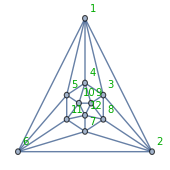
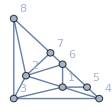
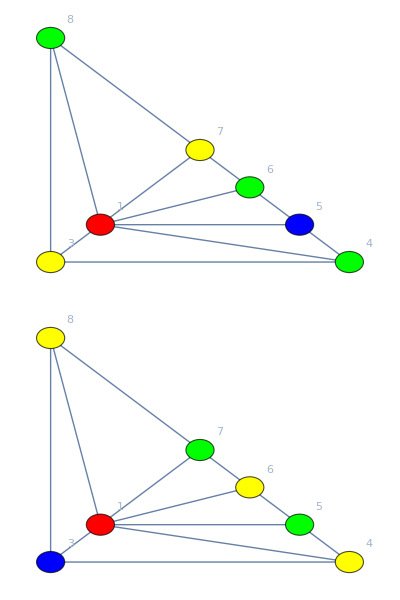
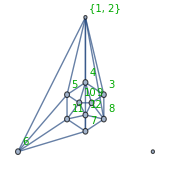
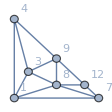
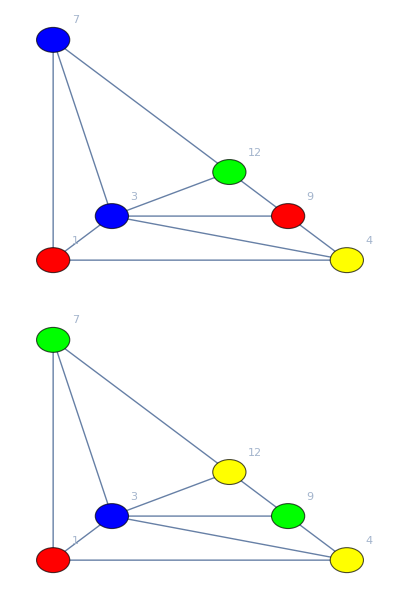
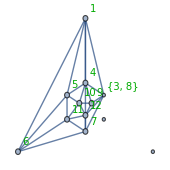
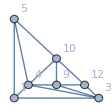
{{-Graphics-{4
24,10,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5},-Graphics-1<->2,-Graphics-},{-Graphics-{4
17,8,1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
6 | 4 | 5 | 5 | 4 | 5 | 5 | 5 | 5 | 5 | 5},-Graphics-3<->8,-Graphics-},{-Graphics-{3
12,8,1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 4 | 5 | 4 | 5 | 5 | 5},-Graphics-4<->9,-Graphics-},{-Graphics-{2
8,2,1 | 3 | 4 | 5 | 6 | 7 | 10 | 11 | 12
5 | 4 | 5 | 5 | 4 | 5 | 4 | 5 | 5},-Graphics-5<->10,-Graphics-},{-Graphics-{2
4,3,1 | 3 | 4 | 5 | 6 | 7 | 11 | 12
5 | 4 | 4 | 5 | 4 | 5 | 4 | 5},-Graphics-6<->11,-Graphics-},{-Graphics-{0
3,5,1 | 3 | 4 | 5 | 6 | 7 | 12
5 | 4 | 4 | 4 | 4 | 4 | 5},-Graphics-7<->12,-Graphics-},{-Graphics-{0
1,1,1 | 3 | 4 | 5 | 6 | 7
5 | 3 | 4 | 4 | 3 | 5},-Graphics-3<->1,-Graphics-},{-Graphics-{0
0,1,1 | 4 | 5 | 6 | 7
4 | 3 | 4 | 3 | 4},-Graphics-5<->4,-Graphics-},{-Graphics-{0
0,1,1 | 4 | 6 | 7
3 | 3 | 3 | 3},-Graphics-7<->6,-Graphics-},{-Graphics-{0
0,1,1 | 4 | 6
2 | 2 | 2},-Graphics-4<->1,-Graphics-}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

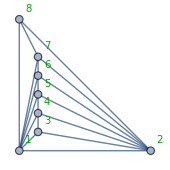
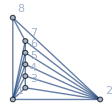
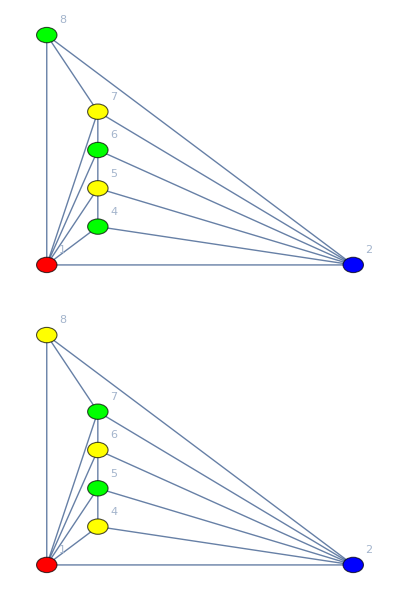
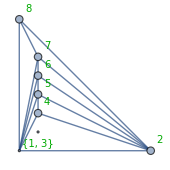
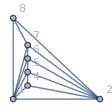
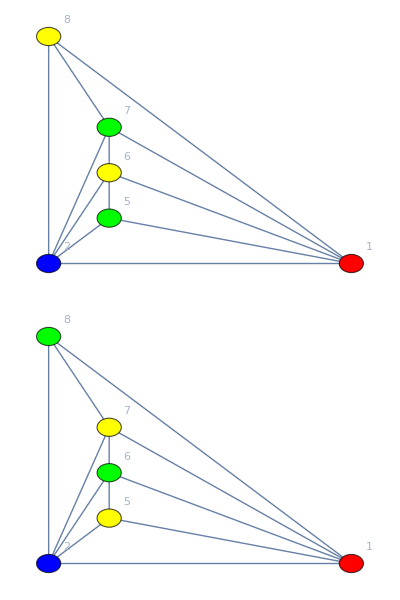
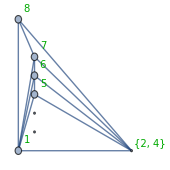
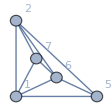
{{-Graphics-{0
6,1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
7 | 7 | 3 | 4 | 4 | 4 | 4 | 3},-Graphics-1<->3,-Graphics-},{-Graphics-{0
3,1,1 | 2 | 4 | 5 | 6 | 7 | 8
6 | 6 | 3 | 4 | 4 | 4 | 3},-Graphics-2<->4,-Graphics-},{-Graphics-{1
0,1,1 | 2 | 5 | 6 | 7 | 8
5 | 5 | 3 | 4 | 4 | 3},-Graphics-5<->6,-Graphics-},{-Graphics-{0
0,1,1 | 2 | 5 | 7 | 8
4 | 4 | 3 | 4 | 3},-Graphics-7<->8,-Graphics-},{-Graphics-{0
0,1,1 | 2 | 5 | 7
3 | 3 | 3 | 3},-Graphics-2<->1,-Graphics-},{-Graphics-{0
0,1,1 | 5 | 7
2 | 2 | 2},-Graphics-7<->5,-Graphics-}}

```mathematica
MpgChain2[MinimalGraph[7] ,"PlanarEmbedding"]
```